```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
ConfigureMaTeX[
"Ghostscript"->"C:\\Program Files\\gs\\gs9.52\\bin\\gswin64c.exe"
]
SetOptions[
#,
Frame -> True,
FrameStyle -> Directive[Black, AbsoluteThickness[1.2], FontSize ->12,FontFamily->"CMU Serif"],
GridLines->Automatic,
ImageSize->Medium,
BaseStyle->{FontFamily->"CMU Serif",FontSize->12}
]&/@{Plot,LogLogPlot,LogPlot,ListLogLogPlot,ListLogPlot,ListLogLinearPlot,ListPlot,ListDensityPlot};

SetOptions[LogPlot,FrameLabel->{Style["x",16],Style["Global Error",16]}];
SetOptions[ListLogLogPlot,FrameLabel->{Style["dt",16],Style["Global Error",16]},PlotMarkers->Automatic,Joined->True,PlotStyle->{Blue,Red,Brown,Orange },PlotLegends->{"x1","x2","x3"}];
LaunchKernels[]
```

{pdfLaTeX→C:\MyPrograms\texlive\2020\bin\win32\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:\Program Files\gs\gs9.52\bin\gswin64c.exe}

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

$Failed

### Analitic

```mathematica
sol=ParametricNDSolve[{x'[t]==-0.1 x[t-2]^2(p-x[t-1]),x[t/;t≤0]==1.5-Cos[t]},x,{t,0,10},{p}]
```

{x→ParametricFunction[<>]}

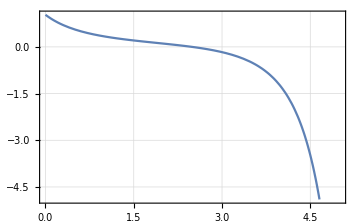

```mathematica
pltAnal=Plot[Evaluate[x[p][10]/.sol],{p,0,5}]
```

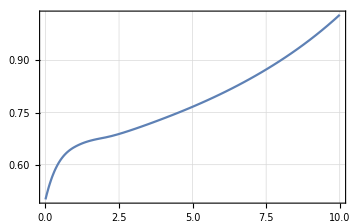

```mathematica
pltAnalC = Plot[Evaluate[x[0][t]/.sol],{t,0,10}]
```

### Calculated

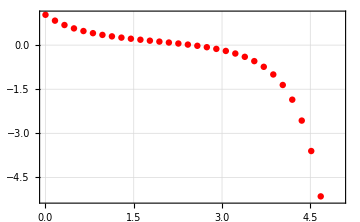

```mathematica
data=Import["logistic.txt","Table","FieldSeparators"->","];
pltMPGOS=ListPlot[data,PlotStyle->Red]
```

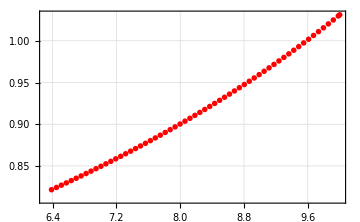

```mathematica
data=Import["DenseOutput_0.txt","Table","FieldSeparators"->","][[13;;,{1,4}]];
pltMPGOSC=ListPlot[data,PlotStyle->Red,PlotRange->All]
```

### Plots

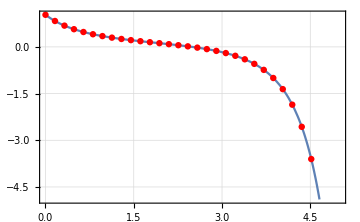

```mathematica
Show[
pltAnal,
pltMPGOS
]
```

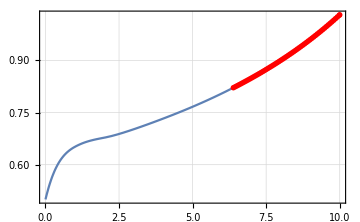

```mathematica
Show[
pltAnalC,
pltMPGOSC
]
```